## Brian — PS 13 — 2025-03-25 — Solution

## EIWL3 Sections 33 and 34

## Exercises from EIWL3 Section 33

```mathematica
(* 33.1 *) Head[ListPlot[{1,2,3}]]
```

Graphics

```mathematica
(* 33.2 *)  Times@@Array[#&,100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
(* 33.3 *) f@@@Tuples[{a,b},2]
```

{f[a,a],f[a,b],f[b,a],f[b,b]}

```mathematica
(* 33.4 *) ExpressionTree/@NestList[#^#&,x,4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 33.5 *) Union[Select[Flatten[Array[#1^2/(#2^2+1)&,{20,20}]],IntegerQ]]
```

{2,5,8,10,17,18,20,32,40,45,50,72,80,98,128,162,200}

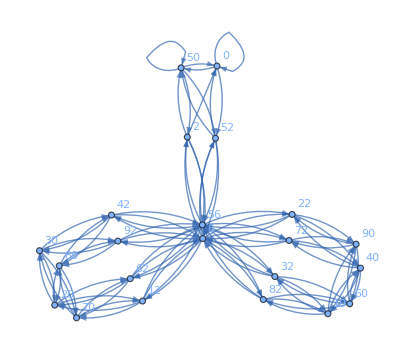

```mathematica
(* 33.6 *) Graph[Rule@@@Partition[Table[Mod[n^2+n,100],{n,100}],2,1],VertexLabels->All]
```

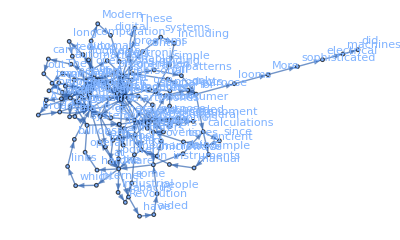

```mathematica
(* 33.7 *) Graph[Rule@@@Partition[Take[TextWords[WikipediaData["computers"]],200],2,1],VertexLabels->All]
```

```mathematica
(* 33.8 *) f@@@{{1,2},{7,2},{5,4}}
```

{f[1,2],f[7,2],f[5,4]}

yields the same result as the more complicated

```mathematica
f@@#&/@{{1,2},{7,2},{5,4}}
```

{f[1,2],f[7,2],f[5,4]}

## Exercises from EIWL3 Section 34

```mathematica
(* 34.1 *)Count[IntegerDigits[3^100],#]&/@Table[i,{i,0,9}]
```

{7,9,9,5,1,5,4,7,0,1}

I think Wolfram’s expected output for Exercise 34.1 is wrong. He fails to include that 8 appears 0 times. His notebook says the expected output is {7,9,9,5,1,5,4,7,1}.

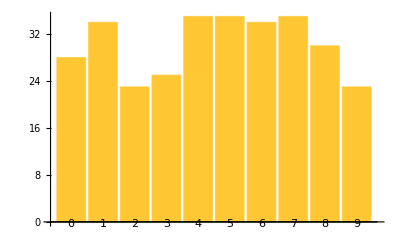

```mathematica
(* 34.2 *) BarChart[Association[#->Count[IntegerDigits[2^1000],#]&/@Table[i,{i,0,9}]],ChartLabels->Table[i,{i,0,9}]]
```

My solution to Exercise 34.2 is a little clunky. Got a better one?

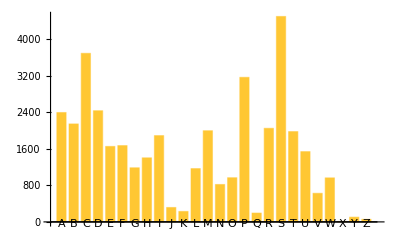

```mathematica
(* 34.3 *) BarChart[Table[Count[Capitalize[First[Characters[#]]]&/@WordList[],letter], {letter,Capitalize/@Alphabet[]}],ChartLabels->Capitalize/@Alphabet[]]
```

Same comment about my solution to Exercise 34.3 as 34.2. I’m guessing there is a slicker way to do these two using associations. In Exercise 34.4 I finally figured out the slicker way.

```mathematica
(* 34.4 *)BarChart[Association[Table[letter->Count[Capitalize[First[Characters[#]]]&/@WordList[],letter], {letter,Capitalize/@Alphabet[]}]],ChartLabels->Automatic]
```

-Graphics-

```mathematica
(* 34.5 *)Count[Characters[WikipediaData["computers"]],#]&/@{"q","u"}//Divide[#[[1]],#[[2]]]&
```

63/1570

My solution to Exercise 34.5 is super-clunky. I may revise this solution after I look at yours :).

```mathematica
(* 34.6 *)Keys[Take[Reverse[Sort[WordCounts[ExampleData[{"Text","AliceInWonderland"}]]]],10]]
```

{the,and,a,to,she,of,was,Alice,in,it}